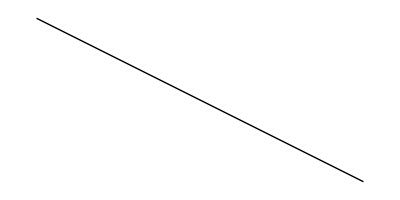
1. naloga
 
d = Daljica[{-1,1},{3,-1}]
d2= Daljica[{-1,-1},{3,1}]
d3= Daljica[{-1,2},{3,0}]
Daljica[{-1,1},{3,-1}]
Daljica[{-1,-1},{3,1}]
Daljica[{-1,2},{3,0}]
Dolzina[Daljica[AA_,BB_]]:= Norm[BB - AA]
Dolzina[d]
2 √5

Slika[Daljica[AA_,BB_]]:=Line[{AA,BB}]
ClearAll
ClearAll
Slika[d]
Line[{{-1,1},{3,-1}}]
Narisi[d_Daljica]:= Graphics[Slika[d]]
Narisi[d]
-Graphics-

EnacbaNosilke[Daljica[AA_,BB_]]:= Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
{x2,y2}=BB;
k =(y2-y1)/(x2-x1);
n = n /. First[Solve[y1==k*x1+n,n]];
y = k*x + n
]
EnacbaNosilke[d]
1/2-x/2

2. naloga

Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA+r(BB-AA) == CC+s(DD-CC),r≥0,r≤1,s≥ 0,s≤1},{r,s}];
If[resitev=={},
{},
First[AA+r(BB-AA)/.resitev]
]]
Presek[d,d3]
{}

3. naloga

```mathematica
m1 = Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
m2 = Append[m1,First[m1]]

Slika[Mnogokotnik[t__]]:=Line[Append[{t},First[{t}]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Narisi[m__Mnogokotnik]:=Graphics[Slika[m]]
```

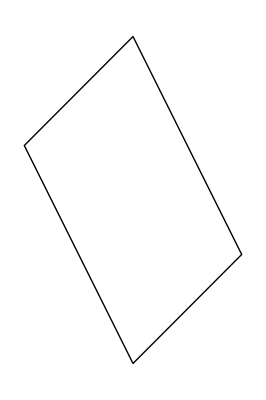

```mathematica
Narisi[m1]
```

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[
{Line
[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],
Point[{0,0}]
}
]
```

```mathematica
PravilniNKotnik[p5]
```

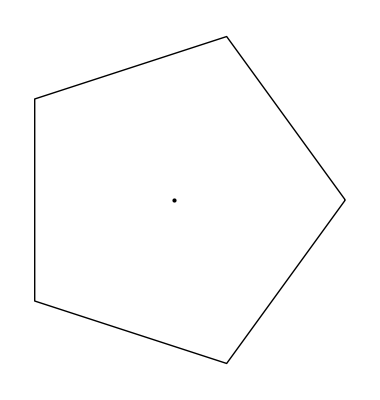
```mathematica
PravilniNKotnik[-Graphics-]
```

```mathematica
PravilniNKotnik[n_,r_,phi_]:= Graphics[
{Line[Table[{r*Cos[(2Pi*i+phi)/n],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],
Point[{0,0}]}
]
pMan = Manipulate[PravilniNKotnik[5,2,phi],{phi,1.5,33}]
```

```mathematica
Daljice[Mnogokotnik[t__]] := Map[Daljica,Partition[{t}, 2,1]]
Daljice[m2]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

4. naloga

```mathematica
Presek2[m_Mnogokotnik,d_Daljica] := Presek[daljice[[1]],d]
```

5. naloga

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
Outer[f,{1,2,3},{4,5,6}]
Flatten[{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}},1]
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[g,m1,m2]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

{f[1,4],f[1,5],f[1,6],f[2,4],f[2,5],f[2,6],f[3,4],f[3,5],f[3,6]}

6. naloga
Dana sta vektorja a in b. Določi takšni števili x in y, da bo vektor c pravokoten tako na vektor a kot na b.

```mathematica
aa = {0, 1, 2}
bb = {1, 2, 3}

cc = {1, x, y}
```

{0,1,2}

{1,2,3}

{1,x,y}

Pravilo da je nek vektor pravokoten na drugega je, da je rezultat njunega skalarnega množenja enak 0. To pravilo uporabimo da dobimo sistem dveh enačb, kateri nato rešimo, da dobimo vrednosti x in y, vektorja c.

```mathematica
Solve[{aa.cc ==0,bb.cc==0},{x,y}]
```

{{x→-2,y→1}}

Z uporabo funkcije solve, smo rešili sistem dveh enačb, kjer smo z “ . “ povedali, da želimo skalarno množenje, saj operiramo z vektorji. Sledi, da je vektor c  =  (1, -2, 1)